```mathematica
SetDirectory[NotebookDirectory[]];
theta = Import["theta.mx"];
tmax = 4761.9;
snapcount = 101;
```

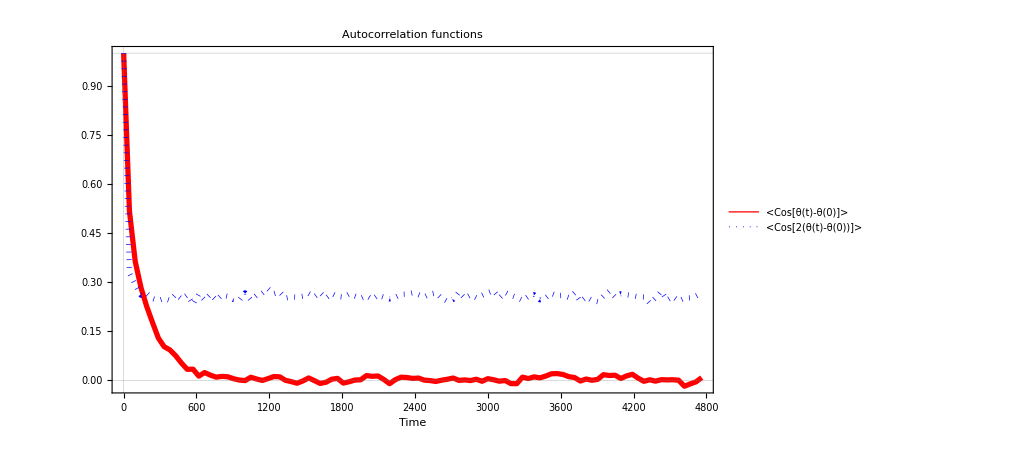

```mathematica
t=Range[0,tmax,tmax/(snapcount-1)];
acor1=Thread[{t,Flatten@(Mean/@{Cos[theta]})}];
acor2=Thread[{t,Flatten@(Mean/@{Cos[2theta]})}];
ListLinePlot[{acor1,acor2},PlotRange->All,GridLines->{{0},{0,1}},Frame->True,PlotLegends->Placed[{Style["<Cos[θ(t)-θ(0)]>",12],Style["<Cos[2(θ(t)-θ(0))]>",12]},{0.75,0.8}],FrameLabel->{Style["Time",14]},PlotLabel->Style["Autocorrelation functions",14],(*PlotMarkers->{{●,8},{▲,8}},*)PlotStyle->{Directive[Red, Thickness[0.005]],Directive[Blue,Dotted,Thickness[0.005]]}]
```